First 25 Entries in the JPL Spectral Line Catalog

The first twenty five entries in the spectral line catalog of the NASA Jet Propulsion Laboratory

This data was aggregated from the JPL website and converted per the specification laid out in the documentation of Herb Pickett’s SPCAT program.

Metadata  |  (Required for public submissions)

Mark Boyer

NASA Jet Propulsion Laboratory

H. M. Pickett, R. L. Poynter, E. A. Cohen, M. L. Delitsky, J. C. Pearson, and H. S. P. Muller, “Submillimeter, Millimeter, and Microwave Spectral Line Catalog,” J. Quant. Spectrosc. & Rad. Transfer 60, 883-890 (1998)

https://spec.jpl.nasa.gov/ftp/pub/catalog/catdir.html

"Agriculture" | "Astronomy" | "Chemistry" | "Computational Universe"
"Computer Systems" | "Culture" | "Demographics" | "Earth Science"
"Economics" | "Education" | "Engineering" | "Geography"
"Geometry Data" | "Government" | "Graphics" | "Health"
"Healthcare" | "History" | "Human Activities" | "Images"
"Language" | "Life Science" | "Literature" | "Machine Learning"
"Manufacturing" | "Mathematics" | "Medicine" | "Meteorology"
"Politics" | "Reference" | "Social Media" | "Sociology"
"Statistics" | "Transportation" |  |

"Audio" | "Entity Store" | "Geospatial Data" | "Graphs"
"Image" | "Numerical Data" | "Text" | "Time Series"

NASA
JPL
spectroscopy

DETAILED SOURCE INFORMATION

$$Object["DefaultContentElement"]="Dataset";

$$Object["FullContent"]=DataResource`$$ContentConversion@
<|
"Dataset"→Dataset@CloudImport@CloudObject[]
|>;

$$Data=$$Object["FullContent"][$$Object["DefaultContentElement"]];

Resource Examples

"ExampleNotebook": 
Examples added here will be included in the example notebook for the resource and will appear on the webpage for the resource. Give examples, including section headings, text and code. Examples should be self-contained, and the simplest examples should be given first. Browse the Data Repository website for examples.

Use subsection cells to divide examples into groups.
Common section names are "Basic Examples", "Visualization" and "Analysis".
Use text cells to provide a brief explanation of each example.

Use $$Data to represent ResourceData[...].
Use $$Object to represent the completed ResourceObject[...].
Use $$Object["FullContent"] to represent ResourceData[...,All].

Be sure to evaluate definitions of $$Data etc. in the Resource Content section. The $$Data etc. symbols will automatically be replaced by ResourceData[...] or ResourceObject, as appropriate, when the output is built.
The symbols in this notebook, including $$Data, have a local context and will not be defined in the Global context. 

Example code: Histogram[$$Data[All,"col1"]]

### Basic Examples

Retrieve the resource:

```mathematica
$$Object
```

$$Object

Retrieve the default content:

```mathematica
$$Data
```

Show the frequency range overlap for the line lists:

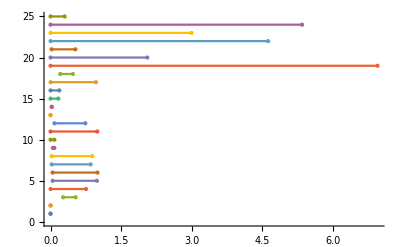

```mathematica
NumberLinePlot[
Interval[QuantityMagnitude/@MinMax@#[[All,"Frequency"]]]&/@Values@Normal@$$Data
]
```

Plot two line lists on the same plot:

```mathematica
ListPlot[
Map[{QuantityMagnitude@#Frequency,#Weight}&]/@RandomSample[Values@Normal@$$Data,2],
Filling->Axis,
PlotMarkers->""
]
```

-Graphics-

$$ResourceObject=ResourceObject[EvaluationNotebook[]]

LocalCache[$$ResourceObject]

LocalObject[file:///Users/markb/Library/Wolfram/Objects/082bdadf-f391-4eaa-a5d4-a8ffd94c50ba]

CloudDeploy[$$ResourceObject,Permissions→"Private"]

CloudDeploy[$$ResourceObject,Permissions→"Public"]

CloudObject[]

CloudDeploy[$$ResourceObject,"Path",Permissions→"Permissions"]

Wolfram

ResourceSubmit[$$ResourceObject]